```mathematica
datas=
Import["/Users/Collin/Fenics/Diffusion/SimpleTests/DirANDNeu/datasavetest.csv","CSV"]
```

{{f_10,Points:0,Points:1,Points:2},{0.000148,-1,0,0},{0.0002213,-0.95833,0,0},{0.00046139,-0.91667,0,0},{0.0010121,-0.875,0,0},4744,{2.2429×10^-57,0.83333,4,0},{-1.0486×10^-56,0.875,4,0},{-3.3547×10^-56,0.91667,4,0},{-2.4047×10^-56,0.95833,4,0},{1.2581×10^-55,1,4,0}}
 |  |  |  |

```mathematica
dataxyv[[3]];
```

```mathematica
InterpolatingFunction
```

```mathematica
dataxyv=Transpose[{Transpose[{datas[[2;;,2]],datas[[2;;,3]]}],datas[[2;;,1]]}]
```

{{{-1,0},0.000148},{{-0.95833,0},0.0002213},{{-0.91667,0},0.00046139},{{-0.875,0},0.0010121},{{-0.83333,0},0.0021597},4743,{{0.83333,4},2.2429×10^-57},{{0.875,4},-1.0486×10^-56},{{0.91667,4},-3.3547×10^-56},{{0.95833,4},-2.4047×10^-56},{{1,4},1.2581×10^-55}}
 |  |  |  |

```mathematica
ifun=Interpolation[dataxyv]
```

InterpolatingFunction[{{-1., 1.}, {0., 4.}}, <>]

```mathematica
Plot3D[ifun[x,y],{x,-1,1},{y,0,4},MeshFunctions->{#3&},RegionFunction->Function[{x,y},-2≤x≤2&&0≤y≤4],BoundaryStyle->Thick,ColorFunction->ColorData[{"Rainbow",{0,2.705}}],ColorFunctionScaling->False,PlotRange->{0,3.01},PlotLegends->BarLegend[{ColorData[{"Rainbow",{0,2.705}}],{0,2.705}},15],ImageSize->Large,AxesLabel->{Style["x (mm)",FontSize->14,FontColor->Black],Style["y (mm)",FontSize->14,FontColor->Black],Style["Concentration 
(cation %)",FontSize->14,FontColor->Black]}]
```

-Graphics3D-

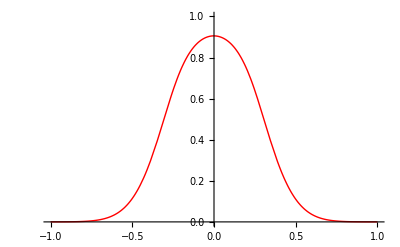

```mathematica
Plot[ifun[x,0.2],{x,-1,1},PlotRange->{0,1}]
```

## Trying to recreate the experimental data with C_s(t) using a 1D recreation

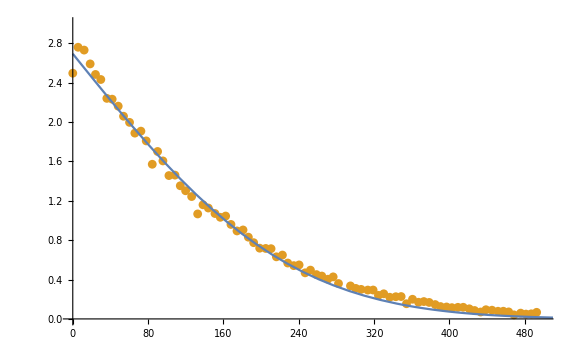

```mathematica
data1d=Import["/Users/Collin/Fenics/Diffusion/ExperimentalRecreation/1D/data1D_ER/Fenics.csv","CSV"];
dataxu=Transpose[{1000*data1d[[2;;,2]],data1d[[2;;,1]]}];
ifun=Interpolation[dataxu];
fitplot=Plot[ifun[x],{x,0,800},PlotRange->All,ImageSize->Large];
dataplot=ListPlot[{Transpose[{datax,datay}]},PlotRange->{{0,500},{0,3}},PlotStyle->ColorData[97,2],Joined->False,FrameTicks->Automatic];
Show[dataplot,fitplot,ImageSize->Large]
```

### Trying to recreate the experimental data with non-linear diffusivity

```mathematica
datas=Import["/Users/Collin/Fenics/Diffusion/NonlinearD/dataDiffFConc/fenics.csv","CSV"];
dataxyv=Transpose[{Transpose[{1000*datas[[2;;,2]],1000*datas[[2;;,3]]}],datas[[2;;,1]]}];
ifun=Interpolation[dataxyv];
fitplot2d=Plot[ifun[0,y],{y,0,800},PlotRange->All,ImageSize->Large];
```

d→4.60955

Co→2.70092

a→0.0164717

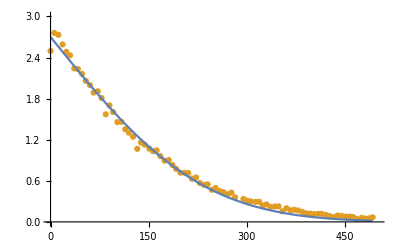

(4.17242 pmCMAS)/pcYSZ

```mathematica
data=Import["/Users/Collin/Research/2016/MicroProbe/April 2016 /Analysis/1300_60_6.csv","CSV"];
Remove[d,Co,a];
Subscript[Co,0]={Co->4}; (*Sets the initial guess for Co, concentration in melt at interface*)
t=58*60; (*Sets experiment time*)
Cc=93.5;
datax=data[[2;;84,13]];
datay=data[[2;;84,9]];
Do[{Subscript[a,n]}=FindRoot[Sqrt[Pi]*a*Exp[a^2]*Erfc[-a]==(Co-0)/(Cc-Co)/.Subscript[Co,n-1],{a,0}]; Model=Co*(Erfc[(x/Sqrt[4*d*t])-a]/Erfc[-a])/.Subscript[a,n];
{Subscript[Co,n],Subscript[d,n]}=FindFit[Transpose[{datax,datay}],{Model,d>0,Co>0},{Co,d},x,MaxIterations->10000],{n,10}];
Print[Subscript[d,10]]
Print[Subscript[Co,10]]
Print[Subscript[a,10]]
plots=Show[ListPlot[{Transpose[{datax,datay}]},PlotRange->{{0,500},{0,3}},PlotStyle->ColorData[97,2],Joined->False,FrameTicks->Automatic],Plot[(Co*(Erfc[(x/Sqrt[4*d*t])-a]/Erfc[-a]))/.{Subscript[a,10],Subscript[Co,10],Subscript[d,10]},{x,0,data[[84,13]]}]]
L=2*a*pmCMAS*Sqrt[d*t]/pcYSZ/.{Subscript[a,10],Subscript[d,10]}
```

### Best fit with some trial and error - parameters are Do=6.2, a=-0.19, Co=2.9

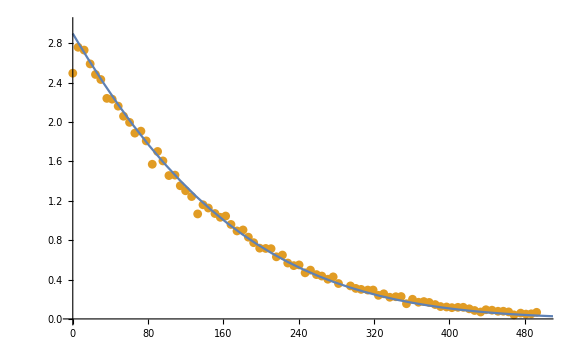

```mathematica
Show[ListPlot[{Transpose[{datax,datay}]},PlotRange->{{0,500},{0,3}},PlotStyle->ColorData[97,2],Joined->False,FrameTicks->Automatic],fitplot,ImageSize->Large]
```

### The same parameters as the plot above, but with a=0.

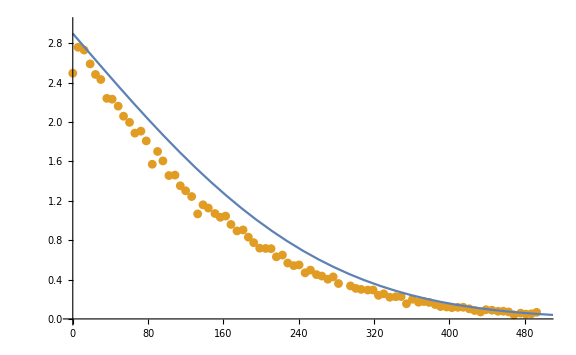

```mathematica
Show[ListPlot[{Transpose[{datax,datay}]},PlotRange->{{0,500},{0,3}},PlotStyle->ColorData[97,2],Joined->False,FrameTicks->Automatic],fitplot,ImageSize->Large]
```

### Parameters with normal fitting method - simulated with FEM. D=4.6, Co = 2.7, a=0

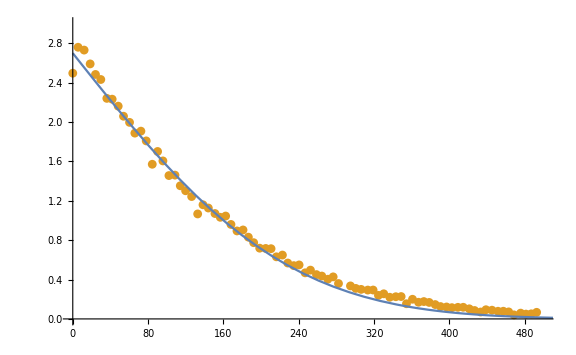

```mathematica
Show[ListPlot[{Transpose[{datax,datay}]},PlotRange->{{0,500},{0,3}},PlotStyle->ColorData[97,2],Joined->False,FrameTicks->Automatic],fitplot,ImageSize->Large]
```

### Adjusting Co to be 2.9, D=4.6

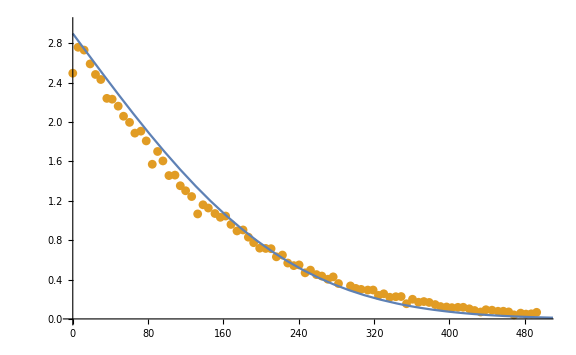

```mathematica
Show[ListPlot[{Transpose[{datax,datay}]},PlotRange->{{0,500},{0,3}},PlotStyle->ColorData[97,2],Joined->False,FrameTicks->Automatic],fitplot,ImageSize->Large]
```

## Messing around with 1-D FEM (Nonlinear)

### FEM based curve fitting method for nonlinear PDEs (diffusion as a function of concentration).

```mathematica
data1d=Import["/Users/Collin/Fenics/Diffusion/NonlinearD/1D/dataDiffFConc/fenics.csv","CSV"];
dataxu=Transpose[{1000*data1d[[2;;,2]],data1d[[2;;,1]]}];
ifun=Interpolation[dataxu];
fitplot=Plot[ifun[x],{x,0,800},PlotRange->All,ImageSize->Large];
```

```mathematica
dataplot=ListPlot[{Transpose[{datax,datay}]},PlotRange->{{0,500},{0,3}},PlotStyle->ColorData[97,2],Joined->False,FrameTicks->Automatic];
```

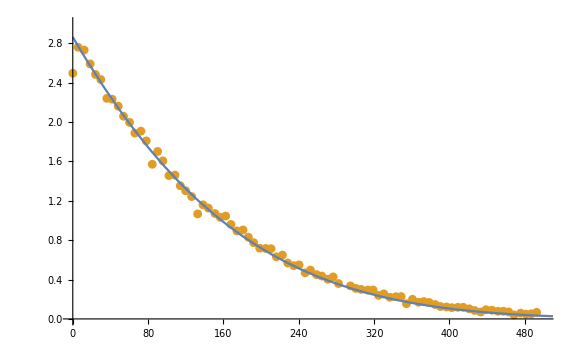

```mathematica
Show[dataplot,fitplot,ImageSize->Large]
```

{10,25,50,100,200,100000}

{9.45,6.414,6.27,6.22,6.196,6.1932}

{-0.57,-0.223,-0.206,-0.199,-0.197,-0.1963}

{2.61,2.82,2.857,2.86,2.86,2.86}

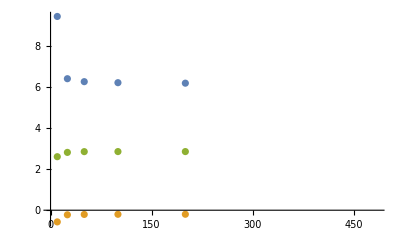

```mathematica
nodes= {10,25, 50, 100, 200,100000} (*Time for 100,000 nodes = 33 min*)
Dd={9.45,6.414,6.27,6.22,6.196,6.1932}
a={-0.57,-0.223,-.206,-0.199,-0.197, -0.1963}
Co={2.61,2.82,2.857,2.86,2.86,2.86}
ListPlot[{Transpose[{nodes,Dd}],Transpose[{nodes,a}],Transpose[{nodes,Co}]}]
```

### GZO 10 min Kramer 1300°C non-linear test

```mathematica
data1d=Import["/Users/Collin/Fenics/Diffusion/NonlinearD/1D/dataDiffFConc/fenics.csv","CSV"];
dataxu=Transpose[{1000*data1d[[2;;,2]],data1d[[2;;,1]]}];
ifun=Interpolation[dataxu];
fitplot=Plot[ifun[x],{x,0,800},PlotRange->All,ImageSize->Large];
```

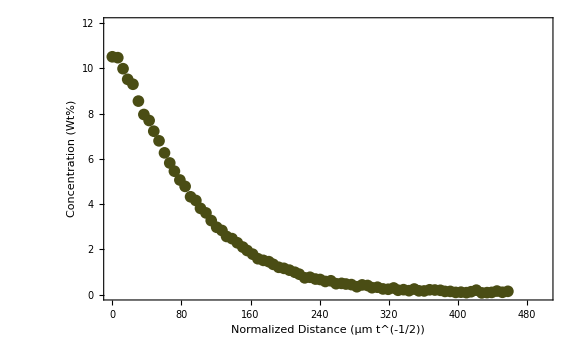

```mathematica
dataplot=ListPlot[{Transpose[{datax,datay}]},PlotRange->{{0,500},{0,12}},PlotStyle->RGBColor["#4a4d14"],Joined->False,FrameTicks->Automatic]
```

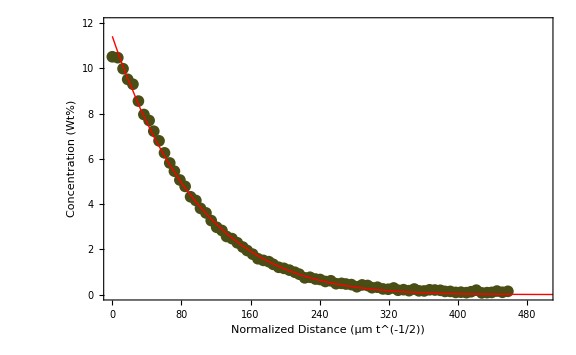

```mathematica
Show[dataplot,fitplot,ImageSize->Large]
```

Looks so fucking good.